```mathematica
(*-----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
Clear[colorfunc,colorfuncOld,rng,P1,TabFibNew,TabFibNewNewFromPiby2Only]
```

```mathematica
TabFibNew=Import["results/WSM/Fermi arc states/plots for paper/WSMTabfibnewdata_up+8_dn+6Irrationalm=4.dat"];
```

```mathematica
TabFibNew
```

{{1.,-3.14159,0.0000917323},{1.85065,-3.14159,0.000267297},{2.37638,-3.14159,0.000761627},{3.22703,-3.14159,0.00124542},4225,{58.4538,3.14159,0.00132423},{58.9796,3.14159,0.00143414},{59.8302,3.14159,0.000846795},{60.6809,3.14159,0.000250579}}
 |  |  |  |

```mathematica
Fibon1D= Import["results/WSM/Fermi arc states/plots for paper/Fibon1D.dat"]
```

{{1.,0},{1.85065,0},{2.37638,0},{3.22703,0},{3.75276,0},{4.60341,0},{5.45407,0},{5.9798,0},{6.83045,0},{7.6811,0},{8.20683,0},{9.05748,0},{9.58321,0},{10.4339,0},{11.2845,0},{11.8102,0},{12.6609,0},{13.5115,0},{14.0373,0},{14.8879,0},{15.4137,0},{16.2643,0},{17.115,0},{17.6407,0},{18.4913,0},{19.0171,0},{19.8677,0},{20.7184,0},{21.2441,0},{22.0948,0},{22.9454,0},{23.4711,0},{24.3218,0},{24.8475,0},{25.6982,0},{26.5488,0},{27.0746,0},{27.9252,0},{28.4509,0},{29.3016,0},{30.1522,0},{30.678,0},{31.5286,0},{32.3793,0},{32.905,0},{33.7557,0},{34.2814,0},{35.132,0},{35.9827,0},{36.5084,0},{37.3591,0},{38.2097,0},{38.7354,0},{39.5861,0},{40.1118,0},{40.9625,0},{41.8131,0},{42.3389,0},{43.1895,0},{43.7152,0},{44.5659,0},{45.4165,0},{45.9423,0},{46.7929,0},{47.6436,0},{48.1693,0},{49.02,0},{49.5457,0},{50.3963,0},{51.247,0},{51.7727,0},{52.6234,0},{53.1491,0},{53.9998,0},{54.8504,0},{55.3761,0},{56.2268,0},{57.0774,0},{57.6032,0},{58.4538,0},{58.9796,0},{59.8302,0},{60.6809,0}}

```mathematica
Dimensions[TabFibNew]
```

{4233,3}

```mathematica
nsiteQuasi = Dimensions[Fibon1D][[1]]
```

83

```mathematica
kzSize = Dimensions[TabFibNew][[1]]/nsiteQuasi
```

51

```mathematica
Fibon1D = Table[{i,0},{i,1 ,nsiteQuasi}]
```

{{1,0},{2,0},{3,0},{4,0},{5,0},{6,0},{7,0},{8,0},{9,0},{10,0},{11,0},{12,0},{13,0},{14,0},{15,0},{16,0},{17,0},{18,0},{19,0},{20,0},{21,0},{22,0},{23,0},{24,0},{25,0},{26,0},{27,0},{28,0},{29,0},{30,0},{31,0},{32,0},{33,0},{34,0},{35,0},{36,0},{37,0},{38,0},{39,0},{40,0},{41,0},{42,0},{43,0},{44,0},{45,0},{46,0},{47,0},{48,0},{49,0},{50,0},{51,0},{52,0},{53,0},{54,0},{55,0},{56,0},{57,0},{58,0},{59,0},{60,0},{61,0},{62,0},{63,0},{64,0},{65,0},{66,0},{67,0},{68,0},{69,0},{70,0},{71,0},{72,0},{73,0},{74,0},{75,0},{76,0},{77,0},{78,0},{79,0},{80,0},{81,0},{82,0},{83,0}}

```mathematica
TabFibNew[[75]]
```

{54.8504,-3.14159,0.00616444}

```mathematica
Do[TabFibNew[[a*nsiteQuasi +b]][[1]] = b,{a,0,kzSize-1},{b,1,nsiteQuasi}]
```

```mathematica
TabFibNew[[84]]
```

{1,-3.01593,0.0000928479}

```mathematica
largestX = Ceiling[Fibon1D[[nsiteQuasi]][[1]]]
```

83

```mathematica
colorfuncOld=Function[{v,vmax},Hue[0.5+0.5*v/vmax,1,1.0-0.3 v/vmax,v/vmax]];
```

```mathematica
rng={0,Max[#]}&@TabFibNew[[All,3]];
```

```mathematica
rng[[2]]
```

0.400618

```mathematica
P1Old = BarLegend[{colorfuncOld[#,rng[[2]]]&,{0,rng[[2]]}},LabelStyle->{Black,FontSize-> 12},Ticks-> {{0,"0.0"},{rng[[2]]/2,"1.0"},{rng[[2]]-10^-3,"2.0"}}]
```

```mathematica
(** Mono color blue **)
```

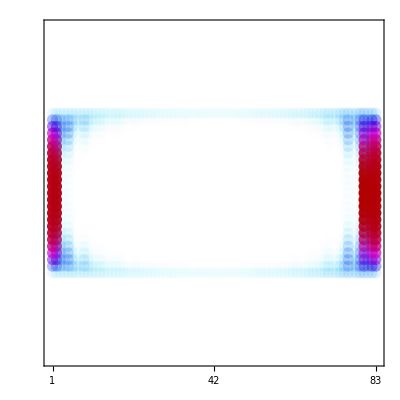

```mathematica
Show[Graphics[{PointSize[0.02],colorfuncOld[#[[3]],rng[[2]]],Point[#[[1;;2]]]}&/@TabFibNewNewFromPiby2Only,
Frame->True,FrameStyle-> Black,
BaseStyle-> 18,
PlotRange-> {{0.5,largestX+0.4},{-π,π}}],
(** ListPlot[Fibon1D,PlotStyle-> {Black,PointSize[0.006]}],**)
FrameTicks->{{{{-π,""},{-π/2,""},{0,""},{π/2,""},{π,""}},None},{{1,{Ceiling[largestX/2],Ceiling[nsiteQuasi/2]},{largestX,nsiteQuasi}},None}},
ImageSize-> 400,AspectRatio->1,RotateLabel->False,FrameStyle->{{Black,Thick},{Black,Thick},{Black,Thick},{Black,Thick}}
]
```

```mathematica
(** Take out the dotted lines from the center --- Also, change the N axis values accordingly to **)
```